#### Test the effect on the heat capacity of a strong perturbation on the harmonic energy eigenspectrum; Testing positive and negative quadratic and linear perturbations of the 1 mode Einstein oscillator heat capacity;

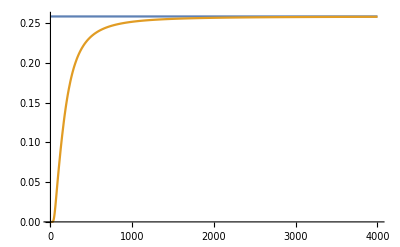

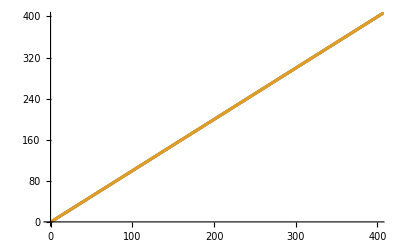

```mathematica
(*Values for one atom PES for 4.685 Angstrom*)
cOmega0=31.58754341976066;
zOmega0=13.44788050977517;
ZanharmonicFit[T_,spectrumZ_,spectrumC_]:={Total[Exp[-2*zOmega0*spectrumZ/(K2meV*T)]],Total[Exp[-2*cOmega0*spectrumC/(K2meV*T)]]}
spectrumharmonicZtest= Table[0.5+x,{x,0,1000}];
spectrumharmonicCtest=Table[0.5+x,{x,0,1000}];
Afittest[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumharmonicZtest,spectrumharmonicCtest]]
Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t},{t,1,4000},PlotRange->All]
ListPlot[{spectrumharmonicCtest,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,400},{0,400}}]
```

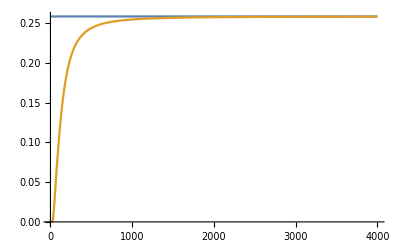

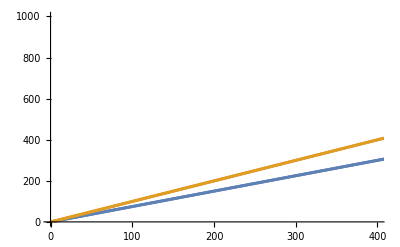

```mathematica
spectrumAnharmonicZtest2= Table[0.5+x-x/4,{x,0,1000}];
spectrumAnharmonicCtest2=Table[0.5+x-x/4,{x,0,1000}];
Afittest2[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZtest2,spectrumAnharmonicCtest2]]
Plot[{K2meV*3,Total[T*D[-D[Afittest2[T],T],T]]/.T->t},{t,1,4000},PlotRange->All]
ListPlot[{spectrumAnharmonicCtest2,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,400},{0,1000}}]
```

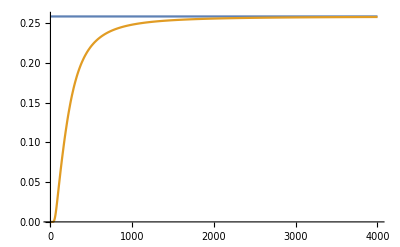

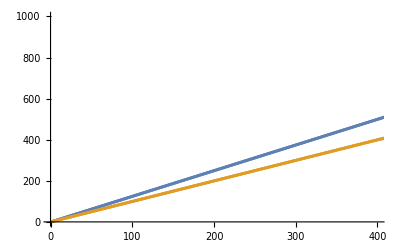

```mathematica
spectrumAnharmonicZtest3= Table[0.5+x+x/4,{x,0,1000}];
spectrumAnharmonicCtest3=Table[0.5+x+x/4,{x,0,1000}];
Afittest3[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZtest3,spectrumAnharmonicCtest3]]
Plot[{K2meV*3,Total[T*D[-D[Afittest3[T],T],T]]/.T->t},{t,1,4000},PlotRange->All]
ListPlot[{spectrumAnharmonicCtest3,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,400},{0,1000}}]
```

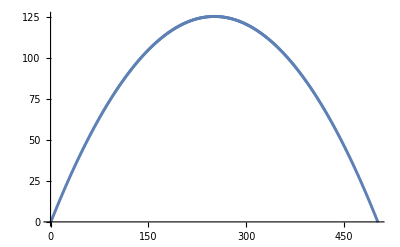

```mathematica
ListPlot[spectrumAnharmonicZtest4]
```

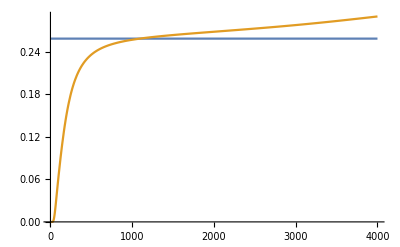

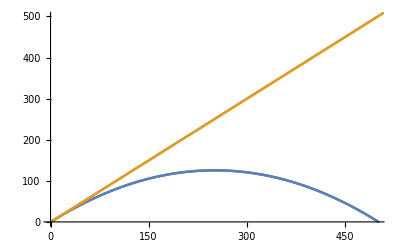

```mathematica
(*The form of perturbation required to produce the beyond haromnic increasing heat capcity behaviour*)
spectrumAnharmonicZtest4= Table[0.5+x-x*x/500,{x,0,500}];
spectrumAnharmonicCtest4=Table[0.5+x-x*x/500,{x,0,500}];Afittest4[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZtest4,spectrumAnharmonicCtest4]]
Plot[{K2meV*3,Total[T*D[-D[Afittest4[T],T],T]]/.T->t},{t,1,4000},PlotRange->All]
ListPlot[{spectrumAnharmonicCtest4,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,500},{0,500}}]
```

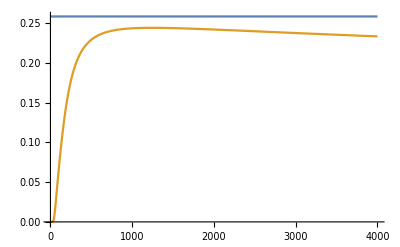

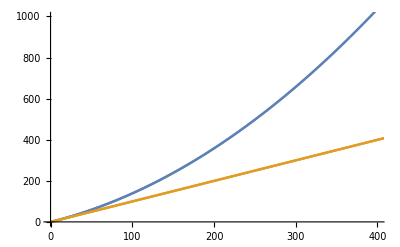

```mathematica
spectrumAnharmonicZtest5= Table[0.5+x+x*x/250,{x,0,1000}];
spectrumAnharmonicCtest5=Table[0.5+x+x*x/250,{x,0,1000}];
Afittest5[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZtest5,spectrumAnharmonicCtest5]]
Plot[{K2meV*3,Total[T*D[-D[Afittest5[T],T],T]]/.T->t},{t,1,4000},PlotRange->All]
ListPlot[{spectrumAnharmonicCtest5,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,400},{0,1000}}]
```

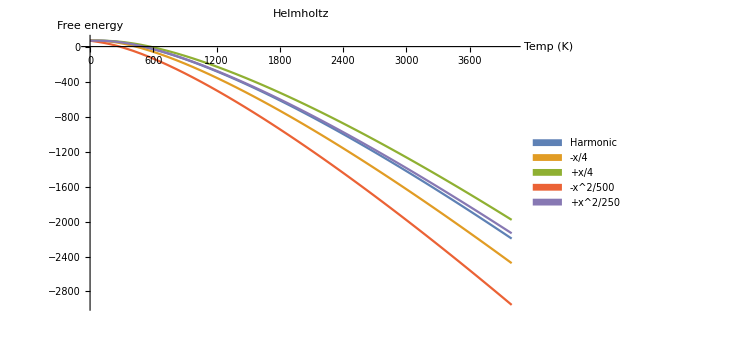

```mathematica
label1={PlotLegends->SwatchLegend[{"Harmonic","-x/4","+x/4","-x^2/500","+x^2/250"}],ImageSize->550,AxesLabel->{"Temp (K)","Free energy"},PlotLabel->"Helmholtz"};
Plot[{Total[Afittest[T]],Total[Afittest2[T]],Total[Afittest3[T]],Total[Afittest4[T]],Total[Afittest5[T]]},{T,1,4000},PlotRange->All,Evaluate@label1]
```

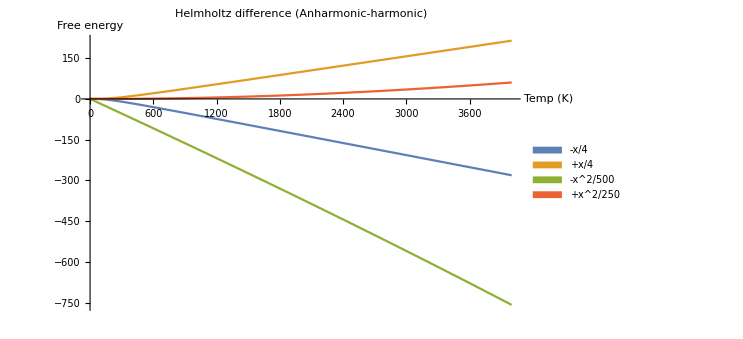

```mathematica
label2={PlotLegends->SwatchLegend[{"-x/4","+x/4","-x^2/500","+x^2/250"}],ImageSize->550,AxesLabel->{"Temp (K)","Free energy"},PlotLabel->"Helmholtz difference (Anharmonic-harmonic)"};
Plot[{Total[Afittest2[T]]-Total[Afittest[T]],Total[Afittest3[T]]-Total[Afittest[T]],Total[Afittest4[T]]-Total[Afittest[T]],Total[Afittest5[T]]-Total[Afittest[T]]},{T,1,4000},PlotRange->All,Evaluate@label2]
```

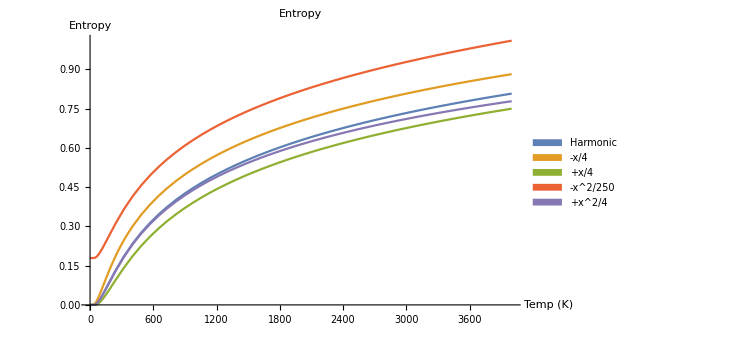

```mathematica
label3={PlotLegends->SwatchLegend[{"Harmonic","-x/4","+x/4","-x^2/250","+x^2/4"}],ImageSize->550,AxesLabel->{"Temp (K)","Entropy"},PlotLabel->"Entropy"};
Plot[{Total[-D[Afittest[T],T]]/.T->t,Total[-D[Afittest2[T],T]]/.T->t,Total[-D[Afittest3[T],T]]/.T->t,Total[-D[Afittest4[T],T]]/.T->t,Total[-D[Afittest5[T],T]]/.T->t},{t,1,4000},PlotRange->All,Evaluate@label3]
```

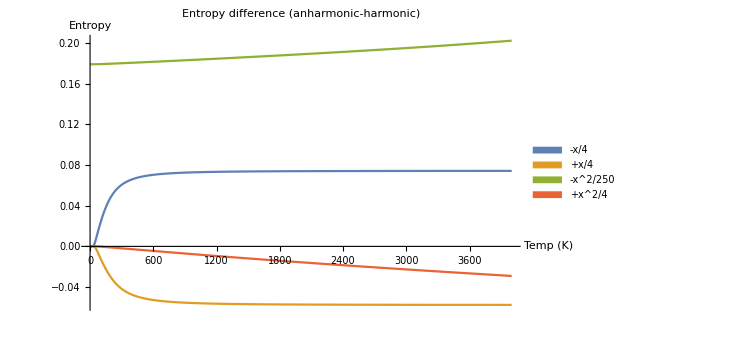

```mathematica
label4={PlotLegends->SwatchLegend[{"-x/4","+x/4","-x^2/250","+x^2/4"}],ImageSize->550,AxesLabel->{"Temp (K)","Entropy"},PlotLabel->"Entropy difference (anharmonic-harmonic)"};
Plot[{(Total[-D[Afittest2[T],T]]-Total[-D[Afittest[T],T]])/.T->t,(Total[-D[Afittest3[T],T]]-Total[-D[Afittest[T],T]])/.T->t,(Total[-D[Afittest4[T],T]]-Total[-D[Afittest[T],T]])/.T->t,(Total[-D[Afittest5[T],T]]-Total[-D[Afittest[T],T]])/.T->t},{t,1,4000},PlotRange->All,Evaluate@label4]
```

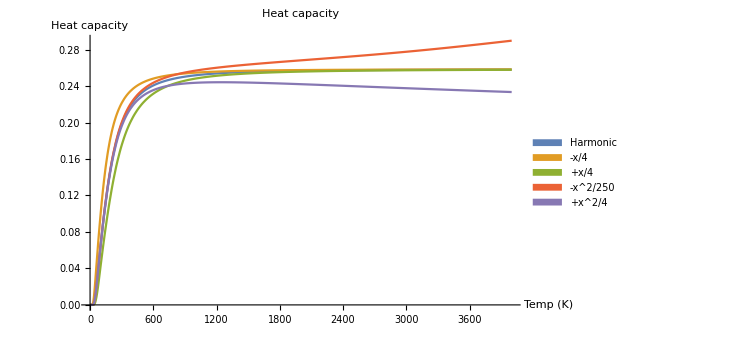

```mathematica
label5={PlotLegends->SwatchLegend[{"Harmonic","-x/4","+x/4","-x^2/250","+x^2/4"}],ImageSize->550,AxesLabel->{"Temp (K)","Heat capacity"},PlotLabel->"Heat capacity"};
Plot[{Total[-T*D[D[Afittest[T],T],T]]/.T->t,Total[-T*D[D[Afittest2[T],T],T]]/.T->t,Total[-T*D[D[Afittest3[T],T],T]]/.T->t,Total[-T*D[D[Afittest4[T],T],T]]/.T->t,Total[-T*D[D[Afittest5[T],T],T]]/.T->t},{t,1,4000},PlotRange->All,Evaluate@label5]
```

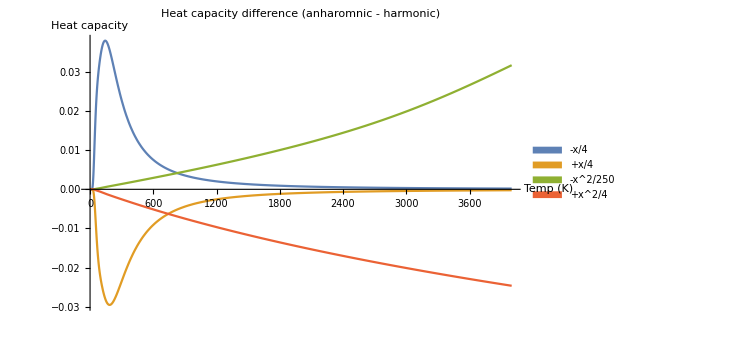

```mathematica
label6={PlotLegends->SwatchLegend[{"-x/4","+x/4","-x^2/250","+x^2/4"}],ImageSize->550,AxesLabel->{"Temp (K)","Heat capacity"},PlotLabel->"Heat capacity difference (anharomnic - harmonic)"};
Plot[{(Total[-T*D[D[Afittest2[T],T],T]]-Total[-T*D[D[Afittest[T],T],T]])/.T->t,(Total[-T*D[D[Afittest3[T],T],T]]-Total[-T*D[D[Afittest[T],T],T]])/.T->t,(Total[-T*D[D[Afittest4[T],T],T]]-Total[-T*D[D[Afittest[T],T],T]])/.T->t,(Total[-T*D[D[Afittest5[T],T],T]]-Total[-T*D[D[Afittest[T],T],T]])/.T->t},{t,1,4000},PlotRange->All,Evaluate@label6]
```

### Test quadratic anharmonic perturbation fit for 4.685Ang Einstein oscillator 2 mode book ;

```mathematica
(*1st order fit*)
z1stPertub4685[x_]:=0.9960212710289351+0.0005106287433996669 x
c1stPertub4685[x_]:=0.9979157732048354+0.0016924565930956804 x
(*2nd order fit*)cPertub4685[x_]:=0.9885913585012485+0.002169997838993376*x-3.3509791469506735*(10^-6)*x*x;
zPertub4685[x_]:=0.9984174011403409+0.0006319656325651873*x-9.38252760109297*(10^-6)*x*x;
(*1st order fit*)
z3rdPertub4685[x_]:=0.9959772085124816+0.0005107179892536683 x+1.5153620885420636*(10^-7) x^2-2.402515100022262*(10^-9) x^3
c3rdPertub4685[x_]:=0.995548605696727+0.0018900026727370505 x-2.79437112245645*(10^-6)x^2+1.8919033818763493*(10^-10) x^3
(*4th order fit*)
c4thPertub4685[x_]:=0.9956918914010281+0.0018520578078129234 x-4.2900457344043634*(10^-7) x^2-5.138635421885797*(10^-8) x^3+3.632080602609196*(10^-10) x^4
z4thPertub4685[x_]:=0.996018011640013+0.0004999125207652784 x+8.251159873028546*(10^-7) x^2-1.7089559647328497*(10^-8)x^3+1.0342989117824144*(10^-10) x^4


cFreqeffective=1;
zFreqeffective=1;
spectrumAnharmonicZtest7= Table[(0.5+x*(zPertub4685[x])),{x,0,360}];
spectrumAnharmonicCtest7=Table[(0.5+x*(cPertub4685[x])),{x,0,360}];
spectrumAnharmonicZtest8= Table[(0.5+x*(z4thPertub4685[x])),{x,0,360}];
spectrumAnharmonicCtest8=Table[(0.5+x*(c4thPertub4685[x])),{x,0,360}];
spectrumAnharmonicZtest11= Table[(0.5+x*(z1stPertub4685[x])),{x,0,360}];
spectrumAnharmonicCtest11=Table[(0.5+x*(c1stPertub4685[x])),{x,0,360}];
spectrumAnharmonicZtest12= Table[(0.5+x*(z3rdPertub4685[x])),{x,0,360}];
spectrumAnharmonicCtest12=Table[(0.5+x*(c3rdPertub4685[x])),{x,0,360}];

Afittest7[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZtest7,spectrumAnharmonicCtest7]]
Afittest8[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZtest8,spectrumAnharmonicCtest8]]
```

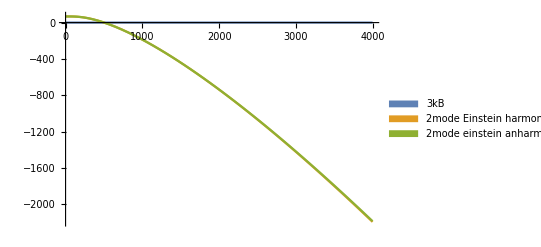

```mathematica
(*2nd order fit free energy*)
Plot[{K2meV*3,Total[Afittest[T]],Total[Afittest7[T]]},{T,1,4000},PlotRange->All,PlotLegends->SwatchLegend[{"3kB","2mode Einstein harmonic","2mode einstein anharmonic"}]]
```

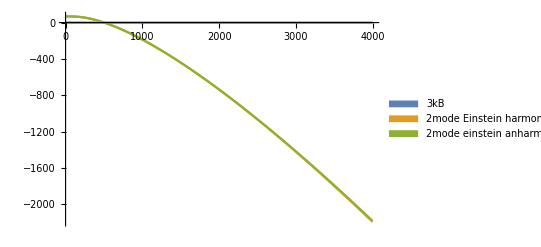

```mathematica
(*4th order fit free energy*)
Plot[{K2meV*3,Total[Afittest[T]],Total[Afittest8[T]]},{T,1,4000},PlotRange->All,PlotLegends->SwatchLegend[{"3kB","2mode Einstein harmonic","2mode einstein anharmonic"}]]
```

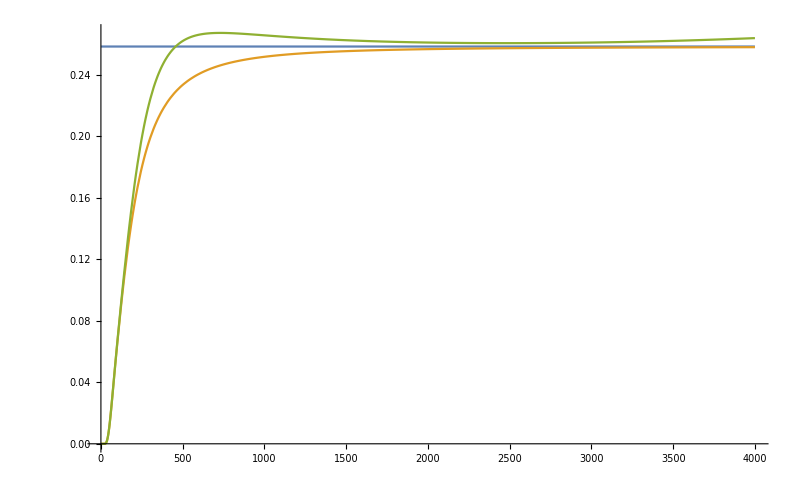

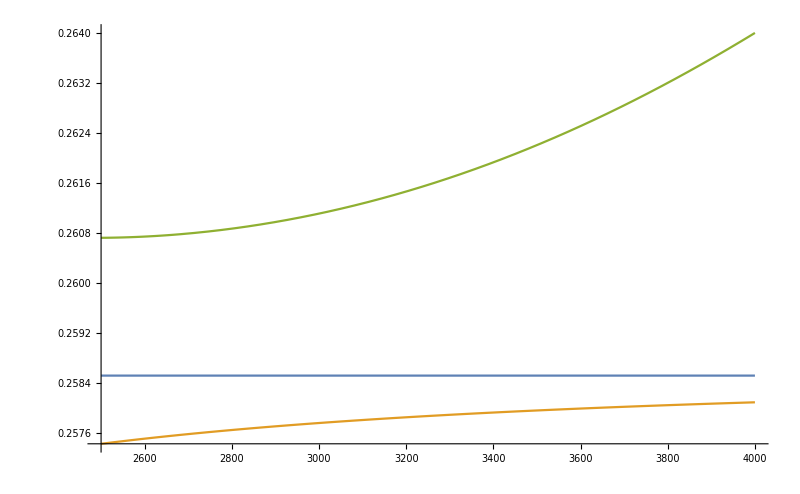

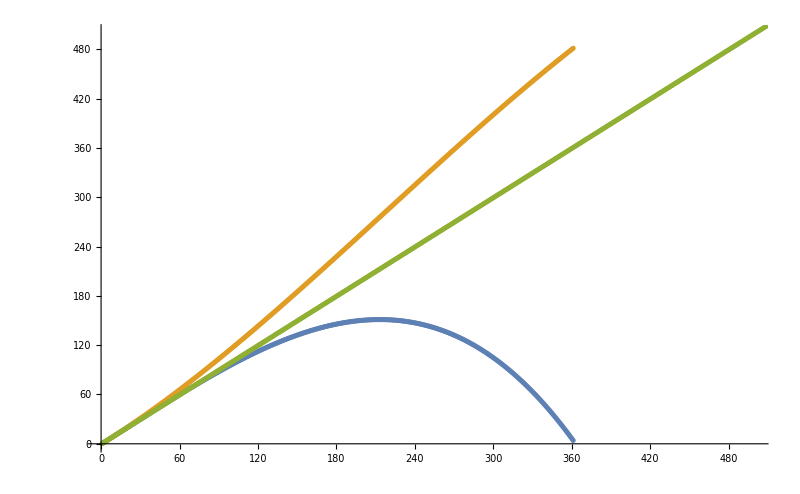

```mathematica
(*Second order perturbation, Heat capacity*)
Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,Total[T*D[-D[Afittest7[T],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800]

Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,Total[T*D[-D[Afittest7[T],T],T]]/.T->t},{t,2500,4000},PlotRange->All,ImageSize->800]

ListPlot[{spectrumAnharmonicZtest7,spectrumAnharmonicCtest7,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,500},{0,500}}]
```

```mathematica
(*4th order perturbation, Heat capacity*)
Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,Total[T*D[-D[Afittest7[T],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800]
```

-Graphics-

```mathematica
(*4th order perturbation, Heat capacity*)
Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,Total[T*D[-D[Afittest7[T],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800]
```

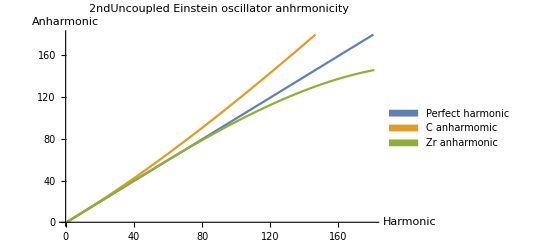

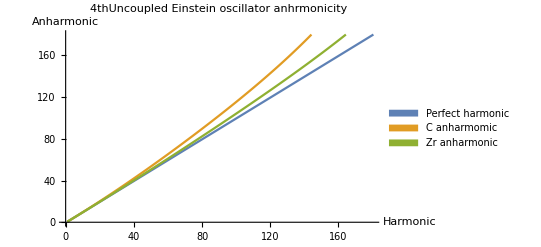

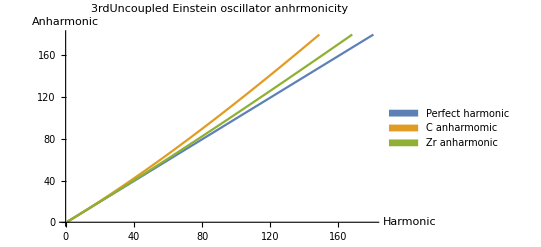

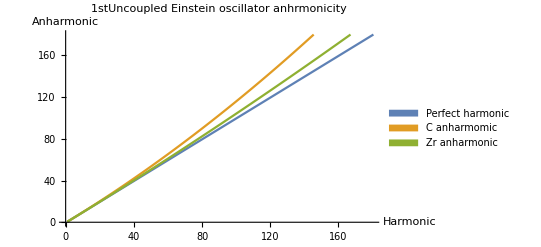

```mathematica
(*2nd order perturbation, eigenspectrum*)
spectrumAnharmonicZtest7= Table[(0.5+x*(zPertub4685[x])),{x,0,180}];
spectrumAnharmonicCtest7=Table[(0.5+x*(cPertub4685[x])),{x,0,180}];
ListPlot[{Table[(0.5+x),{x,0,180}],spectrumAnharmonicCtest7,spectrumAnharmonicZtest7},PlotRange->{{0,180},{0,180}},Joined->True,PlotLegends->SwatchLegend[{"Perfect harmonic","C anharmomic","Zr anharmonic"}],PlotLabel->"2ndUncoupled Einstein oscillator anhrmonicity",AxesLabel->{"Harmonic","Anharmonic"}]

(*4th order perturbation, eigenspectrum*)
spectrumAnharmonicZtest8= Table[(0.5+x*(z4thPertub4685[x])),{x,0,360}];
spectrumAnharmonicCtest8=Table[(0.5+x*(c4thPertub4685[x])),{x,0,360}];
ListPlot[{Table[(0.5+x),{x,0,180}],spectrumAnharmonicCtest8,spectrumAnharmonicZtest8},PlotRange->{{0,180},{0,180}},Joined->True,PlotLegends->SwatchLegend[{"Perfect harmonic","C anharmomic","Zr anharmonic"}],PlotLabel->"4thUncoupled Einstein oscillator anhrmonicity",AxesLabel->{"Harmonic","Anharmonic"}]

(*3rd order perturbation, eigenspectrum*)
spectrumAnharmonicZtest12= Table[(0.5+x*(z3rdPertub4685[x])),{x,0,360}];
spectrumAnharmonicCtest12=Table[(0.5+x*(c3rdPertub4685[x])),{x,0,360}];
ListPlot[{Table[(0.5+x),{x,0,180}],spectrumAnharmonicCtest12,spectrumAnharmonicZtest12},PlotRange->{{0,180},{0,180}},Joined->True,PlotLegends->SwatchLegend[{"Perfect harmonic","C anharmomic","Zr anharmonic"}],PlotLabel->"3rdUncoupled Einstein oscillator anhrmonicity",AxesLabel->{"Harmonic","Anharmonic"}]

(*1st order perturbation, eigenspectrum*)
spectrumAnharmonicZtest11= Table[(0.5+x*(z1stPertub4685[x])),{x,0,360}];
spectrumAnharmonicCtest11=Table[(0.5+x*(c1stPertub4685[x])),{x,0,360}];
ListPlot[{Table[(0.5+x),{x,0,180}],spectrumAnharmonicCtest11,spectrumAnharmonicZtest11},PlotRange->{{0,180},{0,180}},Joined->True,PlotLegends->SwatchLegend[{"Perfect harmonic","C anharmomic","Zr anharmonic"}],PlotLabel->"1stUncoupled Einstein oscillator anhrmonicity",AxesLabel->{"Harmonic","Anharmonic"}]
```

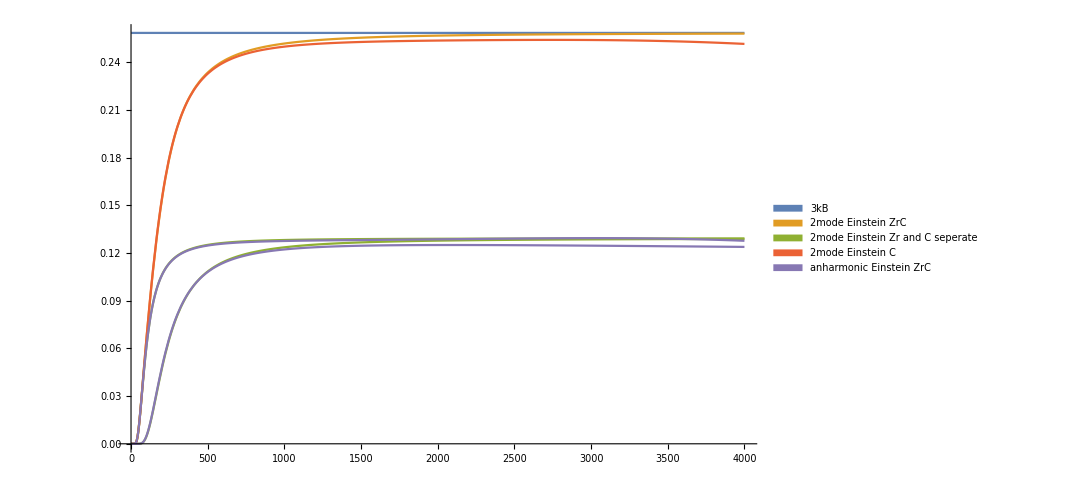

```mathematica
Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,T*D[-D[Afittest[T],T],T]/.T->t,Total[T*D[-D[Afittest7[T],T],T]]/.T->t,T*D[-D[Afittest7[T],T],T]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLegends->SwatchLegend[{"3kB","2mode Einstein ZrC","2mode Einstein Zr and C seperate","2mode Einstein C","anharmonic Einstein ZrC","anharmonic Einstein Zr and C separate"}]]
```

### Test quadratic and 4th order anharmonic perturbation fit for 4.801Ang Einstein oscillator 2 mode book ;

```mathematica
(*2nd order fit*)
cPertub4801[x_]:=0.9885913585012485+0.002169997838993376 x-3.3509791469506735*(10^-6) x^2;

zPertub4801[x_]:=0.9984174011403409+0.0006319656325651873 x-9.38252760109297*(10^-8)x^2;
(*4th order fit*)
c4thPertub4801[x_]:=0.9887068776434652+0.002135082914340699 x-9.842707449044008*(10^-7) x^2-5.462098445724934*(10^-8) x^3+4.0071979789888677*(10^-10) x^4;
z4thPertub4801[x_]:=0.9985351720972293+0.0006075497278408529 x+1.1302146329924996*(10^-6) x^2-2.1964768538460546*(10^-8) x^3+1.2951613601885178*(10^-10) x^4;


cFreqeffective=1;
zFreqeffective=1;
spectrumAnharmonicZtest9= Table[((0.5+x)*(zPertub4801[x])),{x,0,360}];
spectrumAnharmonicCtest9=Table[((0.5+x)*(cPertub4801[x])),{x,0,360}];
spectrumAnharmonicZtest10= Table[((0.5+x)*(z4thPertub4801[x])),{x,0,360}];
spectrumAnharmonicCtest10=Table[((0.5+x)*(c4thPertub4801[x])),{x,0,360}];

Afittest9[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZtest9,spectrumAnharmonicCtest9]]
Afittest10[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZtest10,spectrumAnharmonicCtest10]]
```

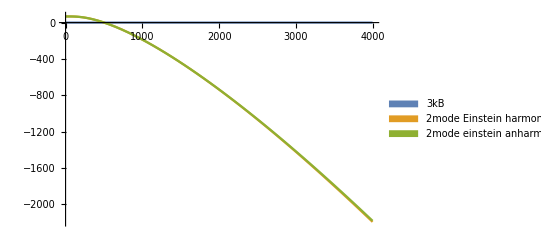

```mathematica
(*2nd order fit free energy*)
Plot[{K2meV*3,Total[Afittest[T]],Total[Afittest9[T]]},{T,1,4000},PlotRange->All,PlotLegends->SwatchLegend[{"3kB","2mode Einstein harmonic","2mode einstein anharmonic"}]]
```

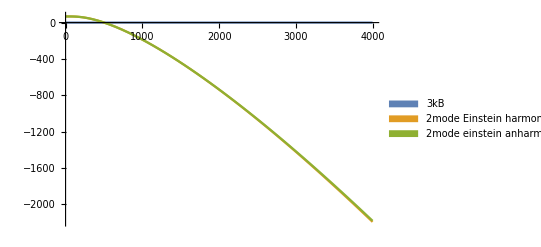

```mathematica
(*4th order fit free energy*)
Plot[{K2meV*3,Total[Afittest[T]],Total[Afittest10[T]]},{T,1,4000},PlotRange->All,PlotLegends->SwatchLegend[{"3kB","2mode Einstein harmonic","2mode einstein anharmonic"}]]
```

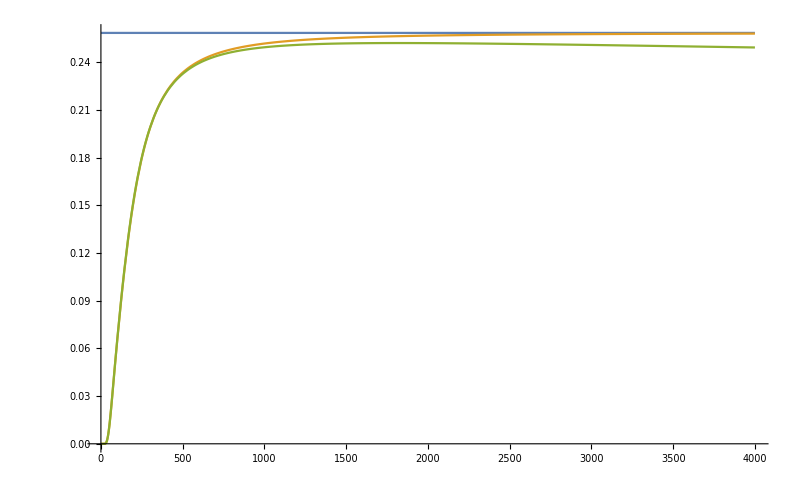

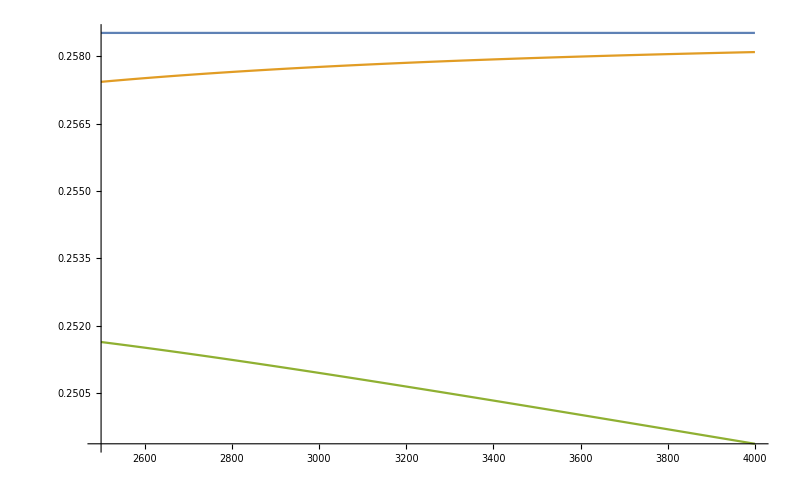

ListPlot::nonopt: Options expected (instead of SwatchLegends[Zr,C,perfect]) beyond position 1 in ListPlot[{{0.5,1.49905,2.49936,3.50094,4.50378,5.50787,6.51323,7.51986,8.52774,9.53688,«31»,42.491,43.5414,44.593,45.6459,46.7,47.7553,48.8119,49.8697,50.9288,«311»},{«1»},{0.5,1.5,«47»,49.5,«951»}},«1»,«1»]. An option must be a rule or a list of rules.

ListPlot[{{0.5,1.49905,2.49936,3.50094,4.50378,5.50787,6.51323,7.51986,8.52774,9.53688,10.5473,11.5589,12.5718,13.586,14.6015,15.6181,16.6361,17.6553,18.6757,19.6974,20.7204,21.7446,22.7701,23.7968,24.8247,25.8539,26.8844,27.9161,28.9491,29.9833,31.0188,32.0555,33.0934,34.1326,35.1731,36.2147,37.2577,38.3019,39.3473,40.3939,41.4418,42.491,43.5414,44.593,45.6459,46.7,47.7553,48.8119,49.8697,50.9288,51.9891,53.0506,54.1133,55.1773,56.2426,57.309,58.3767,59.4457,60.5158,61.5872,62.6599,63.7337,64.8088,65.8851,66.9626,68.0414,69.1214,70.2026,71.2851,72.3688,73.4537,74.5398,75.6271,76.7157,77.8055,78.8965,79.9888,81.0822,82.1769,83.2728,84.3699,85.4683,86.5678,87.6686,88.7706,89.8738,90.9782,92.0839,93.1907,94.2988,95.4081,96.5186,97.6303,98.7432,99.8574,100.973,102.089,103.207,104.326,105.446,106.568,107.69,108.814,109.939,111.065,112.193,113.321,114.451,115.582,116.714,117.848,118.982,120.118,121.255,122.394,123.533,124.674,125.816,126.959,128.103,129.248,130.395,131.543,132.692,133.842,134.993,136.146,137.3,138.455,139.611,140.768,141.927,143.087,144.248,145.41,146.573,147.738,148.903,150.07,151.238,152.408,153.578,154.75,155.922,157.096,158.272,159.448,160.625,161.804,162.984,164.165,165.347,166.531,167.716,168.901,170.088,171.276,172.466,173.656,174.848,176.041,177.235,178.43,179.626,180.824,182.023,183.223,184.424,185.626,186.829,188.034,189.24,190.446,191.655,192.864,194.074,195.286,196.498,197.712,198.927,200.144,201.361,202.58,203.799,205.02,206.242,207.465,208.69,209.915,211.142,212.37,213.599,214.829,216.06,217.293,218.526,219.761,220.997,222.234,223.472,224.712,225.952,227.194,228.437,229.68,230.926,232.172,233.419,234.668,235.918,237.168,238.42,239.674,240.928,242.183,243.44,244.698,245.956,247.216,248.478,249.74,251.003,252.268,253.534,254.8,256.068,257.338,258.608,259.879,261.152,262.425,263.7,264.976,266.253,267.531,268.811,270.091,271.373,272.656,273.939,275.224,276.51,277.798,279.086,280.376,281.666,282.958,284.251,285.545,286.84,288.136,289.434,290.732,292.032,293.332,294.634,295.937,297.241,298.547,299.853,301.16,302.469,303.779,305.089,306.401,307.714,309.028,310.344,311.66,312.978,314.296,315.616,316.937,318.259,319.582,320.906,322.231,323.558,324.885,326.214,327.543,328.874,330.206,331.539,332.873,334.208,335.545,336.882,338.221,339.56,340.901,342.243,343.586,344.93,346.275,347.621,348.969,350.317,351.667,353.017,354.369,355.722,357.076,358.431,359.787,361.144,362.502,363.861,365.222,366.584,367.946,369.31,370.675,372.041,373.408,374.776,376.145,377.515,378.886,380.259,381.632,383.007,384.383,385.759,387.137,388.516,389.896,391.277,392.659,394.043,395.427,396.812,398.199,399.586,400.975,402.365,403.756,405.147,406.54,407.934,409.329,410.726,412.123,413.521,414.92,416.321,417.722,419.125,420.529,421.933,423.339,424.746,426.154,427.563,428.973,430.384,431.796,433.209,434.624,436.039,437.455},{0.5,1.49076,2.48584,3.48521,4.48887,5.49679,6.50894,7.52532,8.5459,9.57065,10.5996,11.6326,12.6698,13.7111,14.7564,15.8058,16.8593,17.9167,18.9782,20.0436,21.113,22.1864,23.2636,24.3448,25.4298,26.5187,27.6114,28.7079,29.8083,30.9124,32.0203,33.1319,34.2472,35.3662,36.4889,37.6153,38.7453,39.8789,41.0161,42.1569,43.3012,44.4491,45.6004,46.7553,47.9137,49.0755,50.2407,51.4094,52.5815,53.7569,54.9357,56.1178,57.3033,58.492,59.684,60.8792,62.0777,63.2795,64.4844,65.6924,66.9037,68.118,69.3355,70.5561,71.7797,73.0064,74.2361,75.4689,76.7046,77.9433,79.185,80.4296,81.6771,82.9275,84.1808,85.4369,86.6959,87.9576,89.2222,90.4895,91.7596,93.0324,94.3079,95.5862,96.867,98.1506,99.4368,100.726,102.017,103.311,104.607,105.906,107.208,108.512,109.818,111.127,112.439,113.753,115.069,116.387,117.708,119.031,120.357,121.685,123.015,124.347,125.682,127.018,128.357,129.699,131.042,132.387,133.735,135.084,136.436,137.79,139.146,140.503,141.863,143.225,144.588,145.954,147.322,148.691,150.062,151.435,152.81,154.187,155.565,156.946,158.328,159.711,161.097,162.484,163.873,165.263,166.655,168.049,169.444,170.841,172.24,173.64,175.041,176.444,177.848,179.254,180.661,182.07,183.48,184.891,186.304,187.718,189.134,190.55,191.968,193.387,194.808,196.229,197.652,199.076,200.501,201.927,203.354,204.783,206.212,207.643,209.074,210.507,211.94,213.375,214.81,216.246,217.684,219.122,220.561,222.001,223.441,224.883,226.325,227.768,229.211,230.656,232.101,233.547,234.993,236.44,237.888,239.337,240.785,242.235,243.685,245.135,246.586,248.038,249.49,250.942,252.395,253.848,255.302,256.756,258.21,259.665,261.12,262.575,264.031,265.486,266.942,268.398,269.855,271.311,272.768,274.224,275.681,277.138,278.595,280.052,281.509,282.966,284.423,285.88,287.337,288.794,290.25,291.707,293.163,294.619,296.076,297.531,298.987,300.442,301.898,303.352,304.807,306.261,307.715,309.169,310.622,312.074,313.527,314.978,316.43,317.881,319.331,320.781,322.23,323.679,325.127,326.575,328.022,329.468,330.914,332.359,333.803,335.246,336.689,338.131,339.572,341.013,342.452,343.891,345.329,346.766,348.202,349.637,351.071,352.504,353.937,355.368,356.798,358.227,359.655,361.082,362.508,363.933,365.356,366.779,368.2,369.62,371.039,372.456,373.873,375.288,376.701,378.114,379.525,380.934,382.343,383.749,385.155,386.559,387.961,389.362,390.762,392.16,393.556,394.951,396.344,397.736,399.126,400.514,401.901,403.286,404.669,406.051,407.43,408.808,410.185,411.559,412.932,414.302,415.671,417.038,418.403,419.766,421.127,422.487,423.844,425.199,426.552,427.903,429.252,430.599,431.944,433.287,434.627,435.965,437.302,438.635,439.967,441.297,442.624,443.949,445.271,446.591,447.909,449.225,450.538,451.849,453.157,454.463,455.766,457.067,458.365,459.661,460.954,462.245,463.533,464.818,466.101,467.381,468.658,469.933,471.205,472.475,473.741,475.005,476.266,477.524,478.779,480.032,481.281},{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5,150.5,151.5,152.5,153.5,154.5,155.5,156.5,157.5,158.5,159.5,160.5,161.5,162.5,163.5,164.5,165.5,166.5,167.5,168.5,169.5,170.5,171.5,172.5,173.5,174.5,175.5,176.5,177.5,178.5,179.5,180.5,181.5,182.5,183.5,184.5,185.5,186.5,187.5,188.5,189.5,190.5,191.5,192.5,193.5,194.5,195.5,196.5,197.5,198.5,199.5,200.5,201.5,202.5,203.5,204.5,205.5,206.5,207.5,208.5,209.5,210.5,211.5,212.5,213.5,214.5,215.5,216.5,217.5,218.5,219.5,220.5,221.5,222.5,223.5,224.5,225.5,226.5,227.5,228.5,229.5,230.5,231.5,232.5,233.5,234.5,235.5,236.5,237.5,238.5,239.5,240.5,241.5,242.5,243.5,244.5,245.5,246.5,247.5,248.5,249.5,250.5,251.5,252.5,253.5,254.5,255.5,256.5,257.5,258.5,259.5,260.5,261.5,262.5,263.5,264.5,265.5,266.5,267.5,268.5,269.5,270.5,271.5,272.5,273.5,274.5,275.5,276.5,277.5,278.5,279.5,280.5,281.5,282.5,283.5,284.5,285.5,286.5,287.5,288.5,289.5,290.5,291.5,292.5,293.5,294.5,295.5,296.5,297.5,298.5,299.5,300.5,301.5,302.5,303.5,304.5,305.5,306.5,307.5,308.5,309.5,310.5,311.5,312.5,313.5,314.5,315.5,316.5,317.5,318.5,319.5,320.5,321.5,322.5,323.5,324.5,325.5,326.5,327.5,328.5,329.5,330.5,331.5,332.5,333.5,334.5,335.5,336.5,337.5,338.5,339.5,340.5,341.5,342.5,343.5,344.5,345.5,346.5,347.5,348.5,349.5,350.5,351.5,352.5,353.5,354.5,355.5,356.5,357.5,358.5,359.5,360.5,361.5,362.5,363.5,364.5,365.5,366.5,367.5,368.5,369.5,370.5,371.5,372.5,373.5,374.5,375.5,376.5,377.5,378.5,379.5,380.5,381.5,382.5,383.5,384.5,385.5,386.5,387.5,388.5,389.5,390.5,391.5,392.5,393.5,394.5,395.5,396.5,397.5,398.5,399.5,400.5,401.5,402.5,403.5,404.5,405.5,406.5,407.5,408.5,409.5,410.5,411.5,412.5,413.5,414.5,415.5,416.5,417.5,418.5,419.5,420.5,421.5,422.5,423.5,424.5,425.5,426.5,427.5,428.5,429.5,430.5,431.5,432.5,433.5,434.5,435.5,436.5,437.5,438.5,439.5,440.5,441.5,442.5,443.5,444.5,445.5,446.5,447.5,448.5,449.5,450.5,451.5,452.5,453.5,454.5,455.5,456.5,457.5,458.5,459.5,460.5,461.5,462.5,463.5,464.5,465.5,466.5,467.5,468.5,469.5,470.5,471.5,472.5,473.5,474.5,475.5,476.5,477.5,478.5,479.5,480.5,481.5,482.5,483.5,484.5,485.5,486.5,487.5,488.5,489.5,490.5,491.5,492.5,493.5,494.5,495.5,496.5,497.5,498.5,499.5,500.5,501.5,502.5,503.5,504.5,505.5,506.5,507.5,508.5,509.5,510.5,511.5,512.5,513.5,514.5,515.5,516.5,517.5,518.5,519.5,520.5,521.5,522.5,523.5,524.5,525.5,526.5,527.5,528.5,529.5,530.5,531.5,532.5,533.5,534.5,535.5,536.5,537.5,538.5,539.5,540.5,541.5,542.5,543.5,544.5,545.5,546.5,547.5,548.5,549.5,550.5,551.5,552.5,553.5,554.5,555.5,556.5,557.5,558.5,559.5,560.5,561.5,562.5,563.5,564.5,565.5,566.5,567.5,568.5,569.5,570.5,571.5,572.5,573.5,574.5,575.5,576.5,577.5,578.5,579.5,580.5,581.5,582.5,583.5,584.5,585.5,586.5,587.5,588.5,589.5,590.5,591.5,592.5,593.5,594.5,595.5,596.5,597.5,598.5,599.5,600.5,601.5,602.5,603.5,604.5,605.5,606.5,607.5,608.5,609.5,610.5,611.5,612.5,613.5,614.5,615.5,616.5,617.5,618.5,619.5,620.5,621.5,622.5,623.5,624.5,625.5,626.5,627.5,628.5,629.5,630.5,631.5,632.5,633.5,634.5,635.5,636.5,637.5,638.5,639.5,640.5,641.5,642.5,643.5,644.5,645.5,646.5,647.5,648.5,649.5,650.5,651.5,652.5,653.5,654.5,655.5,656.5,657.5,658.5,659.5,660.5,661.5,662.5,663.5,664.5,665.5,666.5,667.5,668.5,669.5,670.5,671.5,672.5,673.5,674.5,675.5,676.5,677.5,678.5,679.5,680.5,681.5,682.5,683.5,684.5,685.5,686.5,687.5,688.5,689.5,690.5,691.5,692.5,693.5,694.5,695.5,696.5,697.5,698.5,699.5,700.5,701.5,702.5,703.5,704.5,705.5,706.5,707.5,708.5,709.5,710.5,711.5,712.5,713.5,714.5,715.5,716.5,717.5,718.5,719.5,720.5,721.5,722.5,723.5,724.5,725.5,726.5,727.5,728.5,729.5,730.5,731.5,732.5,733.5,734.5,735.5,736.5,737.5,738.5,739.5,740.5,741.5,742.5,743.5,744.5,745.5,746.5,747.5,748.5,749.5,750.5,751.5,752.5,753.5,754.5,755.5,756.5,757.5,758.5,759.5,760.5,761.5,762.5,763.5,764.5,765.5,766.5,767.5,768.5,769.5,770.5,771.5,772.5,773.5,774.5,775.5,776.5,777.5,778.5,779.5,780.5,781.5,782.5,783.5,784.5,785.5,786.5,787.5,788.5,789.5,790.5,791.5,792.5,793.5,794.5,795.5,796.5,797.5,798.5,799.5,800.5,801.5,802.5,803.5,804.5,805.5,806.5,807.5,808.5,809.5,810.5,811.5,812.5,813.5,814.5,815.5,816.5,817.5,818.5,819.5,820.5,821.5,822.5,823.5,824.5,825.5,826.5,827.5,828.5,829.5,830.5,831.5,832.5,833.5,834.5,835.5,836.5,837.5,838.5,839.5,840.5,841.5,842.5,843.5,844.5,845.5,846.5,847.5,848.5,849.5,850.5,851.5,852.5,853.5,854.5,855.5,856.5,857.5,858.5,859.5,860.5,861.5,862.5,863.5,864.5,865.5,866.5,867.5,868.5,869.5,870.5,871.5,872.5,873.5,874.5,875.5,876.5,877.5,878.5,879.5,880.5,881.5,882.5,883.5,884.5,885.5,886.5,887.5,888.5,889.5,890.5,891.5,892.5,893.5,894.5,895.5,896.5,897.5,898.5,899.5,900.5,901.5,902.5,903.5,904.5,905.5,906.5,907.5,908.5,909.5,910.5,911.5,912.5,913.5,914.5,915.5,916.5,917.5,918.5,919.5,920.5,921.5,922.5,923.5,924.5,925.5,926.5,927.5,928.5,929.5,930.5,931.5,932.5,933.5,934.5,935.5,936.5,937.5,938.5,939.5,940.5,941.5,942.5,943.5,944.5,945.5,946.5,947.5,948.5,949.5,950.5,951.5,952.5,953.5,954.5,955.5,956.5,957.5,958.5,959.5,960.5,961.5,962.5,963.5,964.5,965.5,966.5,967.5,968.5,969.5,970.5,971.5,972.5,973.5,974.5,975.5,976.5,977.5,978.5,979.5,980.5,981.5,982.5,983.5,984.5,985.5,986.5,987.5,988.5,989.5,990.5,991.5,992.5,993.5,994.5,995.5,996.5,997.5,998.5,999.5,1000.5}},PlotRange→{{0,500},{0,500}},SwatchLegends[Zr,C,perfect]]

```mathematica
(*Second order perturbation, Heat capacity*)
Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,Total[T*D[-D[Afittest9[T],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800]

Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,Total[T*D[-D[Afittest9[T],T],T]]/.T->t},{t,2500,4000},PlotRange->All,ImageSize->800]

ListPlot[{spectrumAnharmonicZtest9,spectrumAnharmonicCtest9,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,500},{0,500}},PlotLegends->SwatchLegend["Zr","C","perfect"]]
```

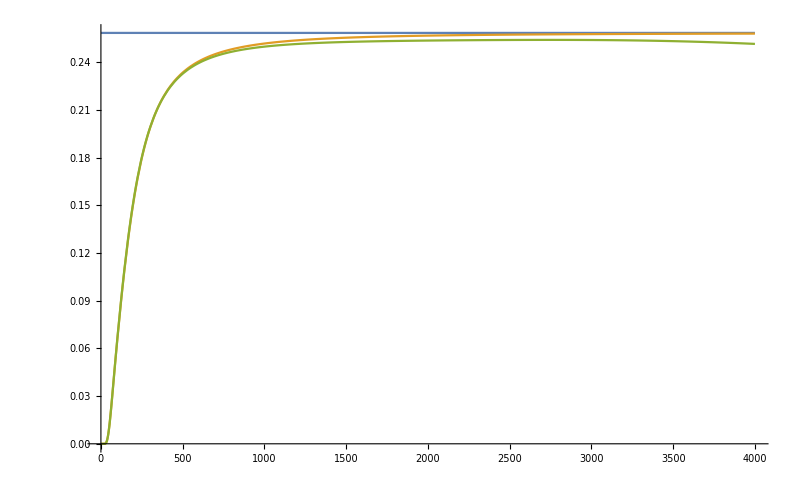

```mathematica
(*4th order perturbation, Heat capacity*)
Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,Total[T*D[-D[Afittest7[T],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800]
```

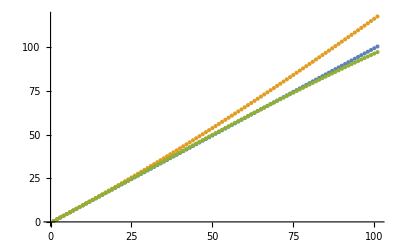

```mathematica
spectrumAnharmonicZtest7= Table[(0.5+x*(zPertub4685[x])),{x,0,100}];
spectrumAnharmonicCtest7=Table[(0.5+x*(cPertub4685[x])),{x,0,100}];
ListPlot@{Table[(0.5+x),{x,0,100}],spectrumAnharmonicCtest7,spectrumAnharmonicZtest7,PlotRange->{{0,100},{0,100}}}
```

```mathematica
Plot[{K2meV*3,Total[T*D[-D[Afittest[T],T],T]]/.T->t,T*D[-D[Afittest[T],T],T]/.T->t,Total[T*D[-D[Afittest7[T],T],T]]/.T->t,T*D[-D[Afittest7[T],T],T]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLegends->SwatchLegend[{"3kB","2mode Einstein ZrC","2mode Einstein Zr and C seperate","2mode Einstein C","anharmonic Einstein ZrC","anharmonic Einstein Zr and C separate"}]]
```

-Graphics-